# Vector borne disease model

## Single infection

```mathematica
Subscript[V, s] = Subscript[Ν, V] - Subscript[V, i];
Subscript[H, s] = Ν - Ι;
dVIdt = Ι Subscript[V, s] γ - α Subscript[V, i] -dv Subscript[V, i];
dIdt = Subscript[V, i]  Subscript[H, s] β - σ Ι - d Ι;
```

```mathematica
Solve[{dVIdt==0, dIdt ==0}, {Subscript[V, i], Ι}]//FullSimplify
```

{{V_i→0,Ι→0},{V_i→(-(dv+α) (d+σ)+β γ Ν Ν_V)/(β (dv+α+γ Ν)),Ι→(-(dv+α) (d+σ)+β γ Ν Ν_V)/(γ (d+σ+β Ν_V))}}

Mutant’s dynamic

```mathematica
dVimdt = Subscript[Ι, m] VSeq Subscript[γ, m] - α Subscript[V, im] - dv Subscript[V, im];
dImdt = Subscript[V, im] Seq Subscript[β, m] - σ Subscript[Ι, m] - d Subscript[Ι, m];
VSeq = Subscript[Ν, V] - VIeq;
Seq = Ν - Ieq;
```

Conventional way of calculating the invasion fitness (based on jacobian matrix)

```mathematica
Jacmatmut = D[{dVimdt, dImdt}, {{Subscript[V, im], Subscript[Ι, m]}}]//FullSimplify;
Jacmatmut//MatrixForm
```

(-dv-α | γ_m (-VIeq+Ν_V)
(-Ieq+Ν) β_m | -d-σ)

```mathematica
fitnessapprox = Det[Jacmatmut]//FullSimplify
```

(dv+α) (d+σ)-(Ieq-Ν) β_m γ_m (VIeq-Ν_V)

```mathematica
selecgrad = D[fitnessapprox/.{Subscript[β, m]-> β[Subscript[x, m]],Subscript[γ, m]-> Subscript[γ, m][Subscript[x, m]]}, Subscript[x, m]]
```

-(Ieq-Ν) (VIeq-Ν_V) γ_m[x_m] β'[x_m]-(Ieq-Ν) (VIeq-Ν_V) β[x_m] γ_m'[x_m]

selection gradient vanishes when
γ[x_m]/β[x_m]= - γ'[x_m]/β'[x_m]

Next generation method to calculate R0 (equivalent to the invasion fitness), just to compare

```mathematica
MM ={ { -α - dv, VSeq Subscript[γ, m]},{Seq Subscript[β, m] , -σ - d}};
Thread[{dVimdt, dImdt}== MM.{Subscript[V, im], Subscript[Ι, m]}]//FullSimplify
MM//MatrixForm
FF = {{0, VSeq Subscript[γ, m]},{0, 0}};
VV = {{α + dv, 0},{- Seq Subscript[β, m], σ + d}};
Eigenvalues[FF.Inverse[VV]]//Simplify
```

{True,True}

(-dv-α | γ_m (-VIeq+Ν_V)
(-Ieq+Ν) β_m | -d-σ)

{0,((Ieq-Ν) β_m γ_m (VIeq-Ν_V))/((dv+α) (d+σ))}

## Multiple infection with two strains

β: transmission from vector to host
γ: transmission from host to vector (Assumption: related to reproduction ability, higher reproduction rate leads to higher number of within host population, hence higher transmission rate to the vector)

```mathematica
(*Naive vectors*)
Sv = Nv - V1 - V2 - V12;
(*Naive hosts*)
Sh = Nh - I1 - I2 - I12;
(*Vectors singly infected with parasite 1*)
dV1dt = γ1 Sv I1  +  γ12 Sv I12  - γ2 V1 I2 - dv V1 - α1 V1;
(*Vectors singly infected with parasite 2*)
dV2dt = γ2 Sv I2 +γ21 Sv I12 - γ1 V2 I1 - dv V2- α2 V2;
(*Vectors coinfected by parasite 1 and 2*)
dV12dt = γ1 V2 I1 + γ2 V1 I2  - dv V12- α12 V12;
(*Hosts singly infected by parasite 1*)
dI1dt = β1 Sh V1  + β12 Sh V12  - β21  I1 V12 - σ1 I1  - dh I1;
(*Hosts singly infected by parasite 2*)
dI2dt = β2 Sh V2 + β21 Sh V12 - β12 I2 V12- σ2 I2 - dh I2;
(*Hosts coinfected by parasite 1 and 2*)
dI12dt = β2 I1 V2 + β1 I2 V1+ β21 I1 V12 + β12 I2 V12 - σ12 I12 - dh I12;
```

```mathematica
odes = {dV1dt, dV2dt, dV12dt, dI1dt, dI2dt, dI12dt};
var = {V1, V2, V12, I1, I2, I12};
```

```mathematica
(*solSim1 = Solve[Thread[odes == 0]/.γ1-> Γ/.γ2-> Γ/.β1-> Β/.β2-> Β/.γ12-> Γ/.β12-> Β/.γ21-> Γ/.β21-> Β, var]*)
```

```mathematica
Solve[Thread[odes==0]/.V2->0/.I2-> 0, var]//FullSimplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{V1→0,V12→0,I1→0,I12→0},{V1→(Nh Nv β1 γ1-(dv+α1) (dh+σ1))/(β1 (dv+α1+Nh γ1)),V12→0,I1→(Nh Nv β1 γ1-(dv+α1) (dh+σ1))/(γ1 (dh+Nv β1+σ1)),I12→0}}

## Numerical analyse of ecological dynamics

## Lesser efficient transmission in coinfection than single infection

```mathematica
vart = {V1[t], V2[t], V12[t], I1[t], I2[t], I12[t]};
sys = Thread[D[vart, t]== (odes/.Thread[var-> vart])];
```

### Changing virulence of the two strains of parasites (coinfection make transmission less efficient and cause more damage)

```mathematica
(* Common parameters for both strains: same transmission rate from host to vector Subscript[γ, i], same transmission rate from vector to host Subscript[β, i], same coinfection transmission rate from host to vector and vice versal
*)commonpar1 = {Nv-> 100, Nh-> 20, γ1 -> 1.5,  γ2 -> 1.5, β1-> 1.45, β2-> 1.45,γ12 -> 0.8,γ21-> 0.8,dv -> 1.1,  β12 -> 0.7, β21-> 0.7, dh -> 1.1};
```

```mathematica
(*Parasite 2 is more virulent than parasite 1 in both vector and host, i.e. α2 > α1, σ2 > σ1, Transmission when parasites are coinfected are less efficient than transmission when parasites are singly infected, i.e. γ1 > γ12, γ2 > γ21, β1 > β12, β2 > β21. Coinfection cause more damage than single infection *)
parVeco1 = { α1-> 0.5,  α2-> 0.9, α12 -> 1.1, σ1-> 0.4, σ2-> 1, σ12 -> 1.2};
```

50

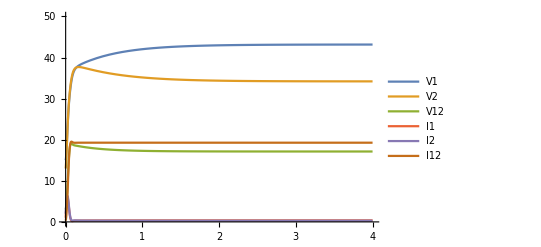

{{43.1628,34.2013,17.1327,0.367752,0.290758,19.275}}

```mathematica
maxtime = 4;
maxpop = 50
init = {V1[0]== 15, V2[0]== 13, V12[0]== 3, I1[0]== 1, I2[0]== 2, I12[0]== 0.3};
sold1 = NDSolve[Join[sys/.commonpar1/.parVeco1, init], vart, {t, 0, maxtime}];
Plot[Evaluate[vart/.sold1], {t, 0, maxtime}, PlotRange->{{0, maxtime},{0, maxpop}}, PlotLegends-> {"V1", "V2", "V12", "I1", "I2", "I12"}]
Evaluate[vart/.sold1]/.t-> maxtime
```

```mathematica
(*Parasite 2 is more virulent than parasite 1 in vector, i.e. α2 > α1, but it is less virulent than parasite 1 in host σ2 < σ1, Transmission when parasites are coinfected are less efficient than transmission when parasites are singly infected, i.e. γ1 > γ12, γ2 > γ21, β1 > β12, β2 > β21. Coinfection cause more damage than single infection *)
parVeco2 = { α1-> 0.5,  α2-> 0.9, α12 -> 1.1, σ1-> 1.2, σ2-> 1, σ12 -> 1.2};
```

50

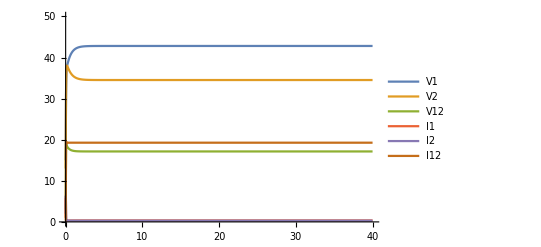

{{42.8194,34.5278,17.145,0.354632,0.301298,19.2756}}

```mathematica
maxtime = 40;
maxpop=50
sold2 = NDSolve[Join[sys/.commonpar1/.parVeco2, init], vart, {t, 0, maxtime}];
Plot[Evaluate[vart/.sold2], {t, 0, maxtime}, PlotRange->{{0, maxtime},{0, maxpop}}, PlotLegends-> {"V1", "V2", "V12", "I1", "I2", "I12"}]
Evaluate[vart/.sold2]/.t-> maxtime
```

```mathematica
minσ1 = 0.1;
maxσ1 = 2;
intvσ1 = 0.1;
numsol1 = Table[NSolve[Thread[odes==0]/.commonpar1/.{α1-> 0.5,  α2-> 0.9, α12 -> 1.1, σ2-> 1, σ12 -> 1.2}, var][[15]], {σ1, minσ1, maxσ1, intvσ1}];
```

```mathematica
numsol1[[10]]
```

{V1→-21.8973,V2→-21.9769,V12→42.2586,I1→-1.37612,I2→-1.44933,I12→2.73485}

```mathematica
Range[minσ1, maxσ1, intvσ1][[10]]
```

1.

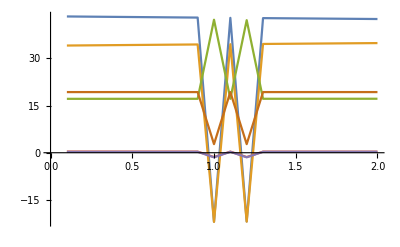

```mathematica
ListPlot[{ V1/.numsol1, V2/.numsol1, V12/.numsol1, I1/.numsol1, I2/.numsol1, I12/.numsol1}, Joined->True, DataRange->{minσ1, maxσ1}]
```

## Mutant’s dynamic of strain 1

```mathematica
dV1mdt = γ1m  𝒱 I1m + γ12m 𝒱 I12m - γ2 I2 V1m - α1 V1m  - dv V1m;
dV12mdt = γ1m V2 I1m +  γ12m V2 I12m + γ2 V1m I2 - α12 V12m - dv V12m;
dI1mdt =  β1m 𝒮 V1m  + β12m 𝒮 V12m  - β21 I1m V12- σ1 I1m  - dh I1m;
dI12mdt = β2 I1m V2 +  β1m  I2 V1m+ β21 I1m V12  + β12m I2 V12m  - σ12 I12m - dh I12m;
```

```mathematica
Mmat = {{- γ2 I2 -α1  - dv, 0, 𝒱 γ1m, 𝒱 γ12m},{γ2 I2, - α12 - dv, γ1m V2, γ12m V2}, {𝒮 β1m, 𝒮 β12m,  - β21 V12- σ1 - dh, 0}, {β1m I2, β12m I2, β2 V2 + β21 V12, -σ12 - dh}};
Thread[{dV1mdt, dV12mdt, dI1mdt, dI12mdt}==Mmat.{V1m, V12m, I1m, I12m}]//FullSimplify
```

{True,True,True,True}

```mathematica
Mmat//MatrixForm
```

(-dv-α1-I2 γ2 | 0 | 𝒱 γ1m | 𝒱 γ12m
I2 γ2 | -dv-α12 | V2 γ1m | V2 γ12m
𝒮 β1m | 𝒮 β12m | -dh-V12 β21-σ1 | 0
I2 β1m | I2 β12m | V2 β2+V12 β21 | -dh-σ12)

The next generation method to calculate R0

```mathematica
Fmat = {{0, 0, 𝒱 γ1m, 𝒱 γ12m},{0, 0, γ1m V2, γ12m V2},{0,0 , 0, 0},{0, 0, 0,0 }};
Vmat = {{α1 + γ2 I2 + dv, 0, 0, 0},{-γ2 I2, α12 + dv, 0, 0},{-𝒮 β1m,-𝒮 β12m, σ1 + β21 V12 + dh, 0},{-β1m I2, -β12m I2, -β2 V2 - β21 V12, σ12 + dh}};
(Mmat == Fmat - Vmat)//FullSimplify
```

True

```mathematica
Fmat.Inverse[Vmat];
Eigenvalues[%][[4]]//Expand;
%/.𝒱 γ12m -> Subscript[ℓ, HV]/.𝒱 γ1m -> HV1mS/.V2 γ1m -> HV1mD/.V2 γ12m -> Subscript[ℒ, HV]/.V2^2 γ12m -> HV12mD V2/.𝒮 β1m -> VH1mS/.𝒮 β12m -> VH12mS/.I2 β1m -> VH1mD/.I2 β12m -> VH12mD/.I2^2 β12m -> VH12mD I2;
Collect[%,Subscript[ℒ, HV] VH12mD]/.(dh dv)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(dh α1)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(dh I2 γ2)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(dv V12 β21)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(V12 α1 β21)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(I2 V12 γ2 β21)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(dv σ1)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(α1 σ1)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(I2 γ2 σ1)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))-> FullSimplify[(dh dv)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(dh α1)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(dh I2 γ2)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(dv V12 β21)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(V12 α1 β21)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(I2 V12 γ2 β21)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(dv σ1)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(α1 σ1)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(I2 γ2 σ1)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))];
Collect[%, HV1mD VH12mS]/.(dh dv)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(dh α1)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(dh I2 γ2)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(dv σ12)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(α1 σ12)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(I2 γ2 σ12)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))-> FullSimplify[(dh dv)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(dh α1)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(dh I2 γ2)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(dv σ12)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(α1 σ12)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(I2 γ2 σ12)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))];
Collect[%, Subscript[ℓ, HV] VH1mD]/.(dh dv)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(dh α12)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(dv V12 β21)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(V12 α12 β21)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(dv σ1)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(α12 σ1)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))-> FullSimplify[(dh dv)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(dh α12)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(dv V12 β21)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(V12 α12 β21)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(dv σ1)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(α12 σ1)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))];
Collect[%, HV1mS VH1mS]/.(dh dv)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(dh α12)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(dv σ12)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(α12 σ12)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))-> FullSimplify[(dh dv)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(dh α12)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(dv σ12)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(α12 σ12)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))];
Collect[%, Subscript[ℓ, HV] I2 VH12mD]/.(dh γ2)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(V12 γ2 β21)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(γ2 σ1)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))-> FullSimplify[(dh γ2)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(V12 γ2 β21)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(γ2 σ1)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))];
Collect[%, HV1mS VH12mS]/.(dh I2 γ2)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(I2 γ2 σ12)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))-> FullSimplify[(dh I2 γ2)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(I2 γ2 σ12)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))];
Collect[%, Subscript[ℒ, HV]  VH12mS]/.(dv V2 β2)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(V2 α1 β2)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(I2 V2 γ2 β2)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(dv V12 β21)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(V12 α1 β21)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(I2 V12 γ2 β21)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))-> FullSimplify[(dv V2 β2)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(V2 α1 β2)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(I2 V2 γ2 β2)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(dv V12 β21)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(V12 α1 β21)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(I2 V12 γ2 β21)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))];
Collect[%, Subscript[ℓ, HV] VH1mS]/.(dv V2 β2)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(V2 α12 β2)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(dv V12 β21)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(V12 α12 β21)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))-> FullSimplify[(dv V2 β2)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(V2 α12 β2)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(dv V12 β21)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))+(V12 α12 β21)/((dv+α12) (dv+α1+I2 γ2) (dh+V12 β21+σ1) (dh+σ12))]/.dv + α12 -> DV12/.dv + α1-> DV1/. dh + σ1 -> DH1/.dh+σ12 -> DH12
```

```mathematica
Subscript[λ, HV] Subscript[ω, HV] Subscript[κ, VH] Subscript[υ, VH] 𝒟 ℳ
```

All death
𝒟 = DH12 = dh + σ12: total death of final host coinfected by both strains
𝒹 = DH1 = dh + σ1: total death of final host infected by strain 1
ℳ = DV12 = dv + α12: total death of vector coinfected by both strains
𝓂 = DV1 = dv + α1: total death of vector coinfected by strain 1

All force of infection (for mutant only) from host to vector
ℓ_HV= HV12mS = 𝒱 γ12m: host coinfected  to naive vector  
ℒ_HV=HV12mD = V2 γ12m: host coinfected to vector infected by strain 2
𝒬_HV=HV1mD = V2 γ1m: host infected by mutant to vector infected by strain 2
𝓆_HV=HV1mS = 𝒱 γ1m: host infected by mutant to naive vector

All force of infection (for mutant only) from vector to host
ℒ_VH=VH1mD = I2 β1m : vector infected by mutant to host infected by strain 2
𝒬_VH=VH12mD = I2 β12m: vector coinfected to host infected by strain 2
ℓ_VH=VH12mS = 𝒮 β12m: vector coinfected to naive host
𝓆_VH=VH1mS = 𝒮 β1m: vector infected by mutant to naive host

Reminder of β and γ
* β is the transmission from vector to host (manipulation of vector can happen here)
* γ is the transmission from host to vector (with parasites that have complex lifecycles this can also be considered the reproduction rate to complete the lifecycle). So there is a trade-off between γ and β, or manipulation and reproduction

So if we consider manipulation as an underlying trade x then γ and β is a function of x and β_1(x) is the transmission rate of strain 1 when it is alone and it depends on the manipulation ability of strain 1 when it is alone, β_12(x) is the transmission rate of strain 1 when it is together with strain 2 and it depends on the manipulation ability of strain 1 when it is with strain 2, γ_1(x) is the reproduction rate of strain 1 when it is alone in the host, and γ_12(x) is the reproduction rate of strain 1 when it is with strain 2 in the host.

The total reproduction ratio of a mutant includes different compartments that represent reproduction values if the mutant follows different routes of infection
Different routes of infection shows the state in which the mutant finds it self

Mutant is alone in both vector and host
 HV1mS/(DV1 + I2 γ2)VH1mS/(DH1 + V12 β21)

Mutant is alone in vector but with strain 2 in host. However, in the host, there are two subscenarios
*Mutant comes after strain 2 in host
ℓ_HV/(DV1 + I2 γ2)VH1mD/DH12
* Mutant comes before strain 2 in host
ℓ_HV/(DV1 + I2 γ2)VH1mS/(DH1 + V12 β21)(V2 β2 + V12 β12)/DH12

Mutant is with strain 2 in vector but alone in host. However, in the vector, there are again two subscenarios
*Mutant comes after strain 2 in vector
 HV1mD/DV12 VH12mS/(DH1 + V12 β21) 
*Mutant comes before strain 2 in vector
HV1mS/(DV1 + I2 γ2)(I2 γ2)/DV12 VH12mS/(DH1 + V12 β12)


Mutant is with strain 2 in both vector and host. Here, there are four subscenarios
Mutant comes after strain 2 in both vector and host
ℒ_HV/DV12 VH12mD/DH12

Mutant comes before strain 2 in both vector and host
 ℓ_HV/(DV1 + I2 γ2)(I2 γ2)/DV12(VH12mS/(DH1 + V12 β12)(V2 β2)/DH12 + VH12mS/(DH1 + V12 β21)(V12 β21)/DV12)

Mutant comes before strain 2 in vector but after strain 2 in host
ℓ_HV/(DV1 + I2 γ2)(I2 γ2)/DV12 VH12mD/DH12

Mutant comes after strain 2 in vector but before strain 2 in host
ℒ_HV/DV12 VH12mS/(DH1 + V12 β21)(V2 β2 + V12 β21)/DH12

Now the manipulating strategy of the mutant strain 1 depends on how we define the function of vector to host (β) and host to vector (γ) transmission. In other words, it depends on how we define the trade-off between transmission (β) and reproduction (γ). Moreover, mutant strategy also depends on the strategy of the other strain in coinfection. Thus, depending on whether manipulation in coinfection boost up or reduce transmission, the mutant may change strategy. Finally, because mutant can either be alone or can be found with another strain, the strategy of the mutant will depends on the available naive hosts and vectors or the already occupied hosts and vectors.